Piecewise[{{0., x≥1||x<0}, {-0.00803994+1.0414 x-0.0748225 x^2+0.216592 x^3, 1/2≤x<1}, {-0.0000169785+1.00039 x-0.00263718 x^2+0.172473 x^3, True}}]

Piecewise[{{0., x≥1||x<0}, {0.985321+0.0798731 x+0.340489 x^2+0.137309 x^3, 1/2≤x<1}, {0.999932+0.00183067 x+0.485748 x^2+0.0421826 x^3, True}}]

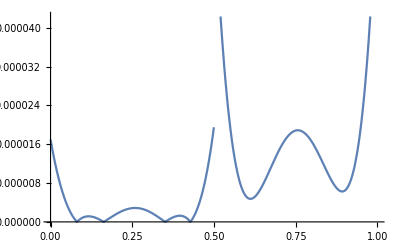

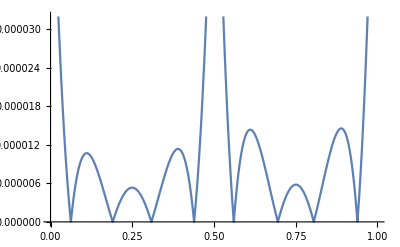

(-0.00002 | 0.99993
0.10017 | 1.00501
0.20133 | 1.02007
0.30452 | 1.04534
0.41075 | 1.08108
0.52103 | 1.12754
0.63665 | 1.18548
0.75857 | 1.25517
0.88809 | 1.33743
1.02651 | 1.4331)

(0.0000169785
9.28988×10^-7
1.5711×10^-6
2.17616×10^-6
1.24925×10^-6
0.0000663413
5.12492×10^-6
0.0000148953
0.000016419
6.44765×10^-6)

(0.0000682587
0.000010303
1.49863×10^-6
1.31942×10^-6
0.000011008
0.0000830804
0.0000138484
8.58969×10^-7
9.67038×10^-7
0.0000140336)

```mathematica
Remove["Global`*"];
ψ[ii_,jj_,x_]:=Module[{},
nh=2ii-1;
Return[Piecewise[{{√(jj+1/2)2^(k/2)LegendreP[jj,2^k x-nh],(nh-1)/2^k≤ x<(nh+1)/2^k}}]];
];
Ψ[x_]:=Flatten[Table[ψ[i,j,x],{i,1,2^(k-1)},{j,0,M-1}]];
DD[P_]:=Module[{},
If[P==0,Return[IdentityMatrix[M*2^(k-1)]]];
H=Table[0,{i,M},{j,M}];
For[r=2,r≤ M,r++,
For[s=1,s≤ r-1,s++,
If[Mod[r+s,2]≠0,
H⟦r,s⟧=2^k √((2r-1)(2s-1));
];
];
];
Return[ArrayFlatten[Table[If[i==j,MatrixPower[H,P],0],{i,1,2^(k-1)},{j,1,2^(k-1)}]]];
];
Q[P_]:=Module[{},
X=W=Table[0,{i,1,M},{j,1,M}];
W ⟦1,1⟧=2;
X⟦1,1⟧=1;X⟦M,M⟧=1;
For[i=1,i< M,i++,
X⟦i,i+1⟧=1/(√(2i-1))1/(√(2i+1));
X⟦i+1,i⟧=-1/(√(2i-1))1/(√(2i+1));
];
Return[MatrixPower[1/2^k ArrayFlatten[Table[If[i==j,X,If[i<j,W,0]],{i,1,2^(k-1)},{j,1,2^(k-1)}]],P]];
];
β[Ι_,S_]:=Module[{ii=Ι,ss=S},
Return[A⟦ii⟧.DD[ss].Ψ[0]];
];

(***************************)
M=4;k=2;
l=2;p=1;
y0={{0},{1}};
yreal[t_]={Sinh[t],Cosh[t]};
AA=1/π∫_0^1 yreal[x]⟦1⟧Ψ[x]ⅆx ;
BB= ∫_0^1 yreal[x]⟦2⟧Ψ[x]ⅆx ;
x0=Join[AA,BB];
(***************************)
 CC=Flatten[Table[Subscript[c, i,j],{i,1,2^(k-1)},{j,0,M-1}]];
A=Table[Flatten[Table[Subscript[a, o,i,j],{i,1,2^(k-1)},{j,0,M-1}]],{o,1,l}];

ans0=Flatten[Simplify[Table[β[i,j]-y0⟦i,j+1⟧,{i,1,l},{j,0,p-1}]]];
(******************)
U[x_]=Integrate[{1-1/2(A⟦2⟧.DD[1].Ψ[t])^2,2t},{t,0,x},Assumptions->0≤ x ≤ 1];
V[x_]=Integrate[ {
 Integrate[ (x-t)(A⟦2⟧.Ψ[t])+( A⟦2⟧.Ψ[t])( A⟦1⟧.Ψ[t]),{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t,
 Integrate[(x-t)(A⟦1⟧.Ψ[t])+ (A⟦1⟧.Ψ[t])^2-( A⟦2⟧.Ψ[t])^2,{t,0,x},Assumptions->0≤ x ≤ 1]/.x->t
},{t,0,x},Assumptions->0≤ x ≤ 1];
eq[x_]=Table[-A⟦i⟧.Ψ[x]+∑_(s=0)^(p-1) y0[[i,s+1]] x^s+U[x]⟦i⟧+V[x]⟦i⟧,{i,1,l}];
xx=Table[(2r-1)/(2^k M),{r,1,2^(k-1)M}];
ANSWER=Table[,{i,1, 2^(k-1)M}];
For[i=1,i≤ 2^(k-1)M,i++,
ANSWER⟦i⟧=eq[xx⟦i⟧];
]; 
javab=Flatten[A]/.FindRoot[Simplify[Flatten[ANSWER]]==0 ,Table[{Flatten[A]⟦i⟧,x0⟦i⟧},{i,1,Length[Flatten[A]]}],MaxIterations->150];
yr1[x_]=Simplify[javab⟦1;;2^(k-1)M⟧.Ψ[x]]
yr2[x_]=Simplify[javab⟦2^(k-1)M+1;;2^(k-1)M*l⟧.Ψ[x]]
Plot[{Abs[yreal[t]⟦1⟧-Re[yr1[t]]]},{t,0,1}]
Plot[{Abs[yreal[t]⟦2⟧-Re[yr2[t]]]},{t,0,1}]
Table[{Round[yr1[i],10^-5],Round[yr2[i],10^-5]},{i,0,0.9,0.1}]//N//MatrixForm
Table[Abs[yr1[i]-yreal[i]⟦1⟧],{i,0,0.9,0.1}]//N//MatrixForm
Table[Abs[yr2[i]-yreal[i]⟦2⟧],{i,0,0.9,0.1}]//N//MatrixForm
```